```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jinyunlin/QFE-Research/QFEgeometry/Mathematica

```mathematica
q3 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q3_summary.txt","Table"];
q4 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q4_summary.txt","Table"];
q5 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q5_summary.txt","Table"];
```

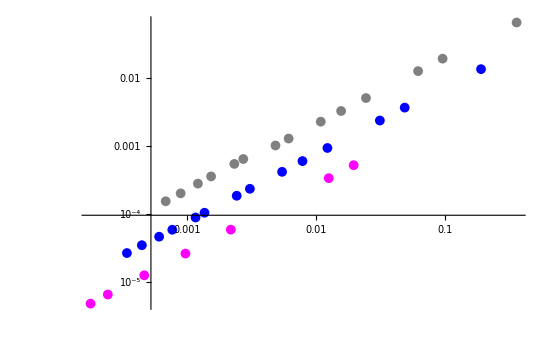

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-5}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-5}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-5}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

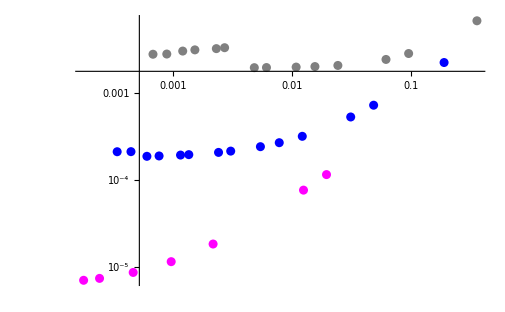

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-4}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-4}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-4}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

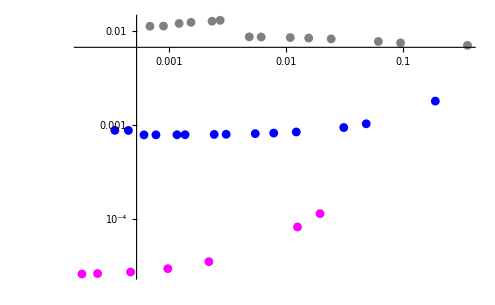

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-3}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-3}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-3}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

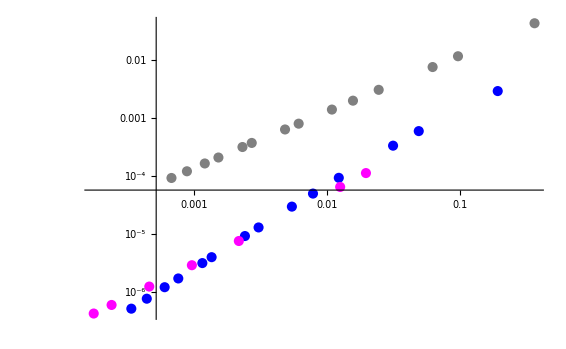

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-2}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-2}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-2}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```